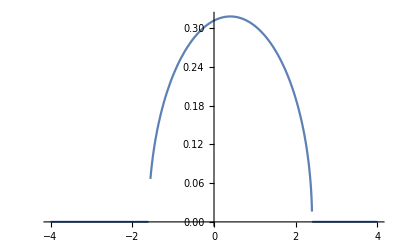

1.

```mathematica
d=2;
ϵ0=0.4;
A[ϵ_]:=UnitStep[d-Abs[ϵ-ϵ0]] 2/(π d^2)Sqrt[d^2-(ϵ-ϵ0)^2];
Plot[A[ϵ],{ϵ,-2d,2d}]
Integrate[A[ϵ],{ϵ,-∞,∞}]
```

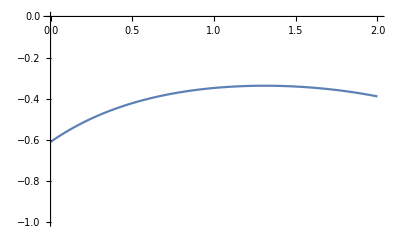

```mathematica
β=2.0;
K[τ_,ϵ_]:=-ⅇ^(-τ ϵ)/(1+ⅇ^(-β ϵ));
G[τ_]:=NIntegrate[K[τ,ϵ]A[ϵ],{ϵ,-∞,∞}];
Plot[G[τ],{τ,0,β},PlotRange->{-1,0}]
```

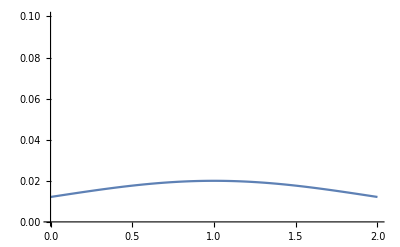

```mathematica
S[τ_]:=0.02Exp[-Abs[τ-β/2]^2/2];
Plot[S[τ],{τ,0,β},PlotRange->{0,0.1}]
```

```mathematica
M=200;
gvals=Table[Re[G[β m/(M-1)]],{m,0,M-1}];
svals=Table[Re[S[β m/(M-1)]],{m,0,M-1}];
```

```mathematica
Export["solution_worker.ref.h5",{gvals,svals,{β}},{"Datasets",{"g_tau","s_tau","beta"}}]
```

solution_worker.ref.h5